## Possibly Useful Identities

Orthogonal:  If Qᵀ.Q=I then dQᵀQ+Qᵀ.dQ=0 and W=Qᵀ.dQ is skew since
	dQᵀQ=-Qᵀ.dQ

Projection:  If P.P=P then dP.P+P.dP=dP and 
	dP.P+P.dP-dP=0
or equivalently 
	dP.(P-I)+P.dP=0
which says with P̂=I-P 
	dP.P̂=P.dP
This one has lots of variants.

Orthogonal Projection:  If P=I-Q.Qᵀ then dP=-dQ.Qᵀ-Q.dQᵀ. Is there anything useful in the structure of the RHS? Well perhaps since
	dP.Q=-dQ.Qᵀ.Q-Q.dQᵀ.Q=-dQ+Q.Qᵀ.dQ=(I-P).dQ
Lots of ways to write this
	dP.Q=P̂.dQ=Q.Qᵀ.dQ=-Q.dQᵀ.Q
Not sure of this is helpful or not.

# Arnoldi AD Implementation

The first couple of sections are working out how to implement AD (1st and 2nd directional derivatives) as an after computation of the Arnoldi computation.

## Arnoldi Code and Test

Note, m is the size of A while n is the depth of the Arnoldi recursion.

```mathematica
Arnoldi[A_][b_,n_]:= Module[
{m=Length[A],Q,H,w,q},
Q=ConstantArray[0.0,{m,n+1}];
H=ConstantArray[0.0,{n+1,n}];
(* Assuming b is normalized! *)
Q⟦All,1⟧=b;
Do[
w=A.Q⟦All,j⟧;
Do[
H⟦k,j⟧=Q⟦All,k⟧.w;
w=w-H⟦k,j⟧ Q⟦All,k⟧,
{k,1,j}];
H⟦j+1,j⟧=Norm[w];
Q⟦All,j+1⟧=w/H⟦j+1,j⟧,
{j,1,n}
];
{Q,H}
]
```

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
b=Normalize[RandomReal[{-1,1},m]];
n=10;
{Q,H}=Arnoldi[A][b,n];
TableForm[{
{UpperTriangularMatrixQ[H,-1],OrthogonalMatrixQ[Q]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}],
{Min[Diagonal[H,-1]],H⟦n+1,n⟧}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},None}]
```

Structure | True | True
Dimensions | True | True
Residuals | 5.05544×10^-16 | 7.6058×10^-16
Subdiagonal | 0.760469 | 0.806137

## Figure of Merit Evolution

Convergence of a block is usually assessed using the figure of merit
	ρ_k=(H_(k+1,k))/(H_(k,k)).
The question is how does this tend to change in synthetic problems.

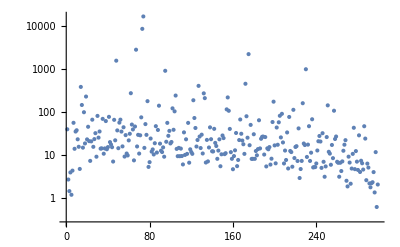

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={6.3,1.2,7.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
ListPlot[ReIm[Eigenvalues[A]]];
b=Normalize[RandomReal[{-1,1},m]];
n=m-1;
{Q,H}=Arnoldi[A][b,n];
ListLogPlot[Diagonal[H,-1]/Abs[Diagonal[H,0]]
]
```

## AD Initialization

I have v_0∈ℝ^n and W=[w_1 | | | w_2 | | | … | | | w_b]∈ℝ^(n×b) with Wᵀ.W=I_b and Wᵀ.v_0=0_b.  The easiest way to make such a thing is by partitioning the orthogonalization of a random n×(b+1)  matrix.  This makes the initialization simple.

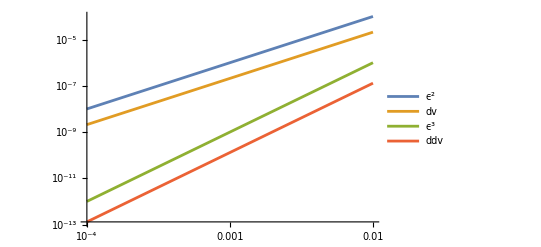

```mathematica
{n,b}={23,4};
vW=QRDecomposition[RandomReal[{-1,1},{n,b+1}]]⟦1⟧ᵀ;
v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
Map[Norm,{Wᵀ.W-IdentityMatrix[b],Wᵀ.v0,v0}];
v[ϵ_]:=(v0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
dv[ϵ_,u1_]:= W.u1(1+ϵ.ϵ)^(-1/2)-(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)ϵ.u1
ddv[ϵ_,u1_,u2_]:=(3(v0+W.ϵ)(1+ϵ.ϵ)^(-5/2)(ϵ.u1 )(ϵ.u2)
-W.u1(1+ϵ.ϵ)^(-3/2)ϵ.u2 -W.u2(1+ϵ.ϵ)^(-3/2)ϵ.u1 -(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)u1.u2
)
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
x0=RandomReal[{-1,1},b];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,b}]];
LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1])],
ϵ^3,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1]+1/2 ϵ^2 ddv[x0,u1,u1])]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","dv","ϵ^3","ddv"}
]
```

Checking that I have first and second derivatives correct in the two direction sense.

```mathematica
g={dv[x0,u1],dv[x0,u2]};
H=({{ddv[x0,u1,u1], ddv[x0,u1,u2]}, {ddv[x0,u2,u1], ddv[x0,u2,u2]}});
{α1,α2}=RandomReal[{-1,1},2];
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
TabView[{
"lin"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g)
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"quad"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g+1/2{ϵ1,ϵ2}.({ϵ1,ϵ2}.H))
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"slice"->LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g )],
ϵ^3,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g+1/2 ϵ^2 {α1,α2}.({α1,α2}.H))]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","lin","ϵ^3","quad"}]
}]
```

123

The Arnoldi process (with no initial scaling) is being defined on the surface of the n-1 dimensional unit sphere 𝒮_(m-1)=∂ℬ_m⊂ℝ^m.  Provided Wᵀ.v_0=0 and Wᵀ.W=I_b the function v:ℬ_b→𝒮_(m-1)⊂ℝ^m defined by 
	v[ϵ]=(v_0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
is a smooth parameterization of a b dimensional patch of 𝒮_(m-1).  The formula above give
	q_1(0) | = | v_0 |   |  
∂_j q_1(0) | = | W.e_j | = | w_j
∂_(j,k) q_1(0) | = | v_0(e_j.e_k) | = | δ_(j,k)v_0
These let us “start” AD computations for the Arnoldi process.

## AD Rewrite

```mathematica
ArnoldiAD[A_][v0_,n_,u1_,u2_]:= Module[
{m=Length[A],Q,dQ1,dQ2,ddQ,H,dH1,dH2,ddH,w,dw1,dw2,ddw},
Q=dQ1=dQ2=ddQ=ConstantArray[0.0,{m,n+1}];
H=dH1=dH2 =ddH=ConstantArray[0.0,{n+1,n}];
(* Initializing derivatives of v[ϵ] from above  *)
(* Assuming v0 is normalized and W = [u1|u2] *)
(* satisfies Wᵀ.v0 = 0 and Wᵀ.W=Subscript[I, 2] *)
Q⟦All,1⟧=v0;dQ1⟦All,1⟧=u1;dQ2⟦All,1⟧=u2;
ddQ⟦All,1⟧=-v0(u1.u2);
(* Differentiating the code.  *)
Do[
w=A.Q⟦All,j⟧;dw1=A.dQ1⟦All,j⟧;dw2=A.dQ2⟦All,j⟧; ddw=A.ddQ⟦All,j⟧;
Do[
(* H and derivatives *)
H⟦k,j⟧=Q⟦All,k⟧.w;
dH1⟦k,j⟧=dQ1⟦All,k⟧.w+Q⟦All,k⟧.dw1;  (* 1st Der 1st var*)
dH2⟦k,j⟧=dQ2⟦All,k⟧.w+Q⟦All,k⟧.dw2;  (* 1st Der 2nd var*)
ddH⟦k,j⟧=ddQ⟦All,k⟧.w+dQ1⟦All,k⟧.dw2+dQ2⟦All,k⟧.dw1+Q⟦All,k⟧.ddw;  (* Mixed 2nd Der *)
(* w and derivatives. *)
w=w-H⟦k,j⟧ Q⟦All,k⟧;
dw1=dw1-dH1⟦k,j⟧ Q⟦All,k⟧-H⟦k,j⟧ dQ1⟦All,k⟧; (* 1st Der 1st var*)
dw2=dw2-dH2⟦k,j⟧ Q⟦All,k⟧-H⟦k,j⟧ dQ2⟦All,k⟧;  (* 1st Der 2nd var*)
ddw=ddw-ddH⟦k,j⟧ Q⟦All,k⟧-dH1⟦k,j⟧*dQ2⟦All,k⟧-dH2⟦k,j⟧*dQ1⟦All,k⟧-H⟦k,j⟧ ddQ⟦All,k⟧;  (* Mixed 2nd Der *),
{k,1,j}];
(* Subdiagonal and Derivatives *)
H⟦j+1,j⟧=(w.w)^(1/2);
dH1⟦j+1,j⟧=(w.w)^(-1/2)(w.dw1);                      (* 1st Der 1st var *)
dH2⟦j+1,j⟧=(w.w)^(-1/2)(w.dw2);                      (* 1st Der 2nd var*)
ddH⟦j+1,j⟧=-(w.w)^(-3/2)(w.dw1)(w.dw2)+(w.w)^(-1/2)(w.ddw+dw1.dw2);(* Mixed 2nd Der *)
(* Final Scaling and Derivatives *)
Q⟦All,j+1⟧=w H⟦j+1,j⟧^-1;
dQ1⟦All,j+1⟧=dw1 H⟦j+1,j⟧^-1-w dH1⟦j+1,j⟧H⟦j+1,j⟧^-2; (* 1st Der 1st var *)
dQ2⟦All,j+1⟧=dw2 H⟦j+1,j⟧^-1-w dH2⟦j+1,j⟧H⟦j+1,j⟧^-2; (* 1st Der 2nd var *)
ddQ⟦All,j+1⟧=ddw H⟦j+1,j⟧^-1 -(dw1*dH2⟦j+1,j⟧+dw2*dH1⟦j+1,j⟧)H⟦j+1,j⟧^-2
+2 w H⟦j+1,j⟧^-3 (dH1⟦j+1,j⟧*dH2⟦j+1,j⟧) -w H⟦j+1,j⟧^-2 ddH⟦j+1,j⟧,  (* Mixed 2nd Der *)
{j,1,n}
];
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}
]
```

Testing.  All appropriate residuals are zero.

```mathematica
{m,b}={56,2};
A=RandomReal[{-1,1},{m,m}];
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2}=Wᵀ;zeros=ConstantArray[0.0,b];
n=11;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,n,u1,u2];
Map[Norm,{A.Q⟦All,1;;n⟧-Q.H,
A.dQ1⟦All,1;;n⟧-dQ1.H-Q.dH1,
A.dQ2⟦All,1;;n⟧-dQ2.H-Q.dH2,
A.ddQ⟦All,1;;n⟧-ddQ.H-dQ1.dH2-dQ2.dH1-Q.ddH}]
Map[Norm,
{dQ1ᵀ.Q+Qᵀ.dQ1,dQ2ᵀ.Q+Qᵀ.dQ2,
ddQᵀ.Q+dQ1ᵀ.dQ2+dQ2ᵀ.dQ1+Qᵀ.ddQ}]
```

{2.16753×10^-15,2.78772×10^-15,2.37745×10^-15,7.23803×10^-15}

{6.63607×10^-16,5.59915×10^-16,1.84443×10^-15}

Testing the whole thing! The first thing to test is the behavior in a single direction

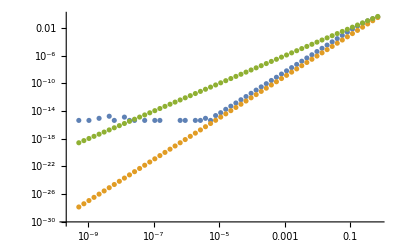

```mathematica
{m,b}={56,2};
A=RandomReal[{-1,1},{m,m}];
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2}=Wᵀ;zeros=ConstantArray[0.0,b];
k=11;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u1];
quad[ϵ1_]= H⟦k+1,k⟧+ ϵ1 dH1⟦k+1,k⟧+0.5 ϵ1^2 ddH⟦k+1,k⟧;
f[ϵ1_,ϵ2_]:=Module[{Q,H},
{Q,H}=Arnoldi[A][(v0+ϵ1 u1+ϵ2 u2)/√(1+ϵ1^2+ϵ2^2),k];
H⟦k+1,k⟧]
ϵ1s=Table[0.7^p,{p, 1,60}];
DataDer=Table[ {ϵ1,Abs[quad[ϵ1]-f[ϵ1,0]]},{ϵ1, ϵ1s}];
DataCube=Table[ {ϵ1,ϵ1^3},{ϵ1, ϵ1s}];
DataSq=Table[ {ϵ1,ϵ1^2},{ϵ1, ϵ1s}];
ListLogLogPlot[{DataDer,DataCube,DataSq}]
```

Building out a 3×3 Hessian and testing random

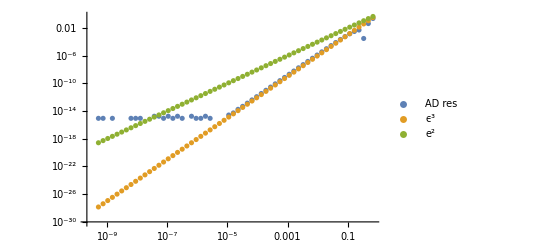

```mathematica
{m,b}={56,3};
A=RandomReal[{-1,1},{m,m}];
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2,u3}=Wᵀ;zeros=ConstantArray[0.0,b];
{grad,Hess}=Map[ConstantArray[0.0,#]&,{3,{3,3}}];
k=11;
(* Fill in the diagonal of Hess *)
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u1];
grad⟦1⟧=dH1⟦k+1,k⟧;Hess⟦1,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u2];
grad⟦2⟧=dH1⟦k+1,k⟧;Hess⟦2,2⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u3,u3];
grad⟦3⟧=dH1⟦k+1,k⟧;Hess⟦3,3⟧=ddH⟦k+1,k⟧;
(* Fill in the off diagonal of Hess *)
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u2];
Hess⟦1,2⟧=Hess⟦2,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u3];
Hess⟦1,3⟧=Hess⟦3,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u3];
Hess⟦2,3⟧=Hess⟦3,2⟧=ddH⟦k+1,k⟧;
Clear[ϵ1,ϵ2,ϵ3,quad,f]
quad[{ϵ1_,ϵ2_,ϵ3_}]=Expand[H⟦k+1,k⟧+grad.{ϵ1,ϵ2,ϵ3}+0.5{ϵ1,ϵ2,ϵ3}.Hess.{ϵ1,ϵ2,ϵ3}];
(* Pick a random direction in the 3D susbapce *)
α=Normalize[RandomReal[{-1,1},3]];
u=α⟦1⟧ u1 +α⟦2⟧ u2 + α⟦3⟧ u3;
f[ϵ_]:=Module[{Q,H},
{Q,H}=Arnoldi[A][(v0+ϵ u)/√(1+ϵ^2),k];
H⟦k+1,k⟧]
ϵs=Table[0.7^p,{p, 1,60}];
DataDer=Table[ {ϵ,Abs[quad[ϵ α]-f[ϵ]]},{ϵ, ϵs}];
DataCube=Table[ {ϵ,ϵ^3},{ϵ, ϵs}];
DataSq=Table[ {ϵ,ϵ^2},{ϵ, ϵs}];
ListLogLogPlot[{DataDer,DataCube,DataSq},PlotLegends->{"AD res","ϵ^3","e^2"}]
```

Everything checks out.

```mathematica
{m,b}={56,3};
A=RandomReal[{-1,1},{m,m}];
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2,u3}=Wᵀ;zeros=ConstantArray[0.0,b];
{grad,Hess}=Map[ConstantArray[0.0,#]&,{3,{3,3}}];
k=11;
(* Fill in the diagonal of Hess *)
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u1];
grad⟦1⟧=dH1⟦k+1,k⟧;Hess⟦1,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u2];
grad⟦2⟧=dH1⟦k+1,k⟧;Hess⟦2,2⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u3,u3];
grad⟦3⟧=dH1⟦k+1,k⟧;Hess⟦3,3⟧=ddH⟦k+1,k⟧;
(* Fill in the off diagonal of Hess *)
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u2];
Hess⟦1,2⟧=Hess⟦2,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u3];
Hess⟦1,3⟧=Hess⟦3,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u3];
Hess⟦2,3⟧=Hess⟦3,2⟧=ddH⟦k+1,k⟧;
Clear[ϵ1,ϵ2,ϵ3,quad,f]
quad[{ϵ1_,ϵ2_,ϵ3_}]=Expand[H⟦k+1,k⟧+grad.{ϵ1,ϵ2,ϵ3}+0.5{ϵ1,ϵ2,ϵ3}.Hess.{ϵ1,ϵ2,ϵ3}];
f[{ϵ1_,ϵ2_,ϵ3_}]:=Module[{Q,H},
{Q,H}=Arnoldi[A][(v0+ϵ1 u1+ϵ2 u2 + ϵ3 u3)/√(1+ϵ1^2+ϵ2^2+ϵ3^2),k];
H⟦k+1,k⟧]
L=0.1;
AbsoluteTiming[
fData3D=Table[f[{ϵ1,ϵ2,ϵ3}],
{ϵ1,-L,L,L/20},{ϵ2,-L,L,L/20},{ϵ3,-L,L,L/20}]/f[{0.0,0.0,0.0}];
qData3D=Table[quad[{ϵ1,ϵ2,ϵ3}],
{ϵ1,-L,L,L/20},{ϵ2,-L,L,L/20},{ϵ3,-L,L,L/20}]/f[{0.0,0.0,0.0}];
]
TabView[{
"f"->ListContourPlot3D[fData3D,
DataRange->{{-L,L},{-L,L},{-L,L}}],
"q"->ListContourPlot3D[qData3D,
DataRange->{{-L,L},{-L,L},{-L,L}}],
"f-q"->ListContourPlot3D[fData3D-qData3D,
Contours->{0.0,0.0001,-0.0001},
ContourStyle->Opacity[0.5],
DataRange->{{-L,L},{-L,L},{-L,L}}
]
},3]
```

{36.8872,Null}

123

Think about the contour pics!

```mathematica
TabView[{
"1,2"->ContourPlot[{f[{ϵ1,ϵ2,0.0}]-quad[{ϵ1,ϵ2,0.0}]},{ϵ1,-L,L},{ϵ2,-L,L},
PerformanceGoal->"Quality",
FrameLabel->{"ϵ1","ϵ2"},
ContourLabels->True,
Contours->40,
Epilog->{Red, PointSize[0.05],Point[{0,0}]}],
"1,3"->ContourPlot[{f[{ϵ1,0.0,ϵ3}]-quad[{ϵ1,0.0,ϵ3}]},{ϵ1,-L,L},{ϵ3,-L,L},
PerformanceGoal->"Quality",
ContourLabels->True,
FrameLabel->{"ϵ1","ϵ3"},
Contours->40,
Epilog->{Red, PointSize[0.05],Point[{0,0}]}],
"2,3"->ContourPlot[{f[{0.0,ϵ2,ϵ3}]-quad[{0.0,ϵ2,ϵ3}]},{ϵ2,-L,L},{ϵ3,-L,L},
PerformanceGoal->"Quality",
FrameLabel->{"ϵ2","ϵ3"},
ContourLabels->True,
Contours->40,
Epilog->{Red, PointSize[0.05],Point[{0,0}]}]
}]
```

123

## Preliminary Small Test

I am making a test problem with three “large” eigenvalues. The natural evolution of the subdiagonal is decreasing.  An initial rapid decrease is due to the separated large eigenvalues.  I have not seen an accidental small value for a sub diagonal.  The scaled values are remarkably consistent!  It is really not “done” until the very end.

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}=10^1{-1.2,1.1,0.6};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
b=Normalize[RandomReal[{-1,1},m]];
{Q,H}=Arnoldi[A][b,m];
TabView[{
"λs"->ListPlot[ReIm[Eigenvalues[A]],PlotRange->All,
PlotLabel->Norm[Eigenvalues[H⟦1;;m,1;;m⟧]-Eigenvalues[A]]],
"H_(k + 1, k)"->ListLogPlot[Diagonal[H,-1],PlotRange->All,GridLines->Automatic,Frame->True],
"H_(k + 1, k)/|H_(k, k)|"->ListLogPlot[Diagonal[H,-1]/Abs[Diagonal[H]],PlotRange->All,GridLines->Automatic,Frame->True]
},2]
```

123

I am going to try running the thing for a depth of k=10 with a 2 search directions.

```mathematica
b=2;
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
{u1,u2}=Wᵀ;
k=10;
DDF=ConstantArray[0.0,{2,2}];
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u1];
DDF⟦1,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u1,u2];
DDF⟦1,2⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u1];
DF={dH1[[k+1,k]],dH2[[k+1,k]]};
DDF⟦2,1⟧=ddH⟦k+1,k⟧;
{{Q,H},{dQ1,dH1},{dQ2,dH2},{ddQ,ddH}}=ArnoldiAD[A][v0,k,u2,u2];
DDF⟦2,2⟧=ddH⟦k+1,k⟧;
F=H⟦k+1,k⟧;
ϵ=1.1;
HGT[{x1_,x2_}]:= Module[{k=10,Q,H},
{Q,H}=Arnoldi[A][(v0+x1 u1 + x2 u2)/√(1+x1^2+x2^2),k];
H⟦k+1,k⟧
]
ϵ=1.1;
TabView[{
"Speed"->ContourPlot[ HGT[{x1,x2}]/F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Speed",
ContourLabels->True,PlotLegends->Automatic],
"Quality"->ContourPlot[ HGT[{x1,x2}]/F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Epilog->{Red, Point[{0,0}],Green,Circle[{0,0},ϵ]},
Contours->20,
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic],
"Quad"->ContourPlot[(0.5 {x1,x2}.DDF.{x1,x2}+DF.{x1,x2}+F)/F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Epilog->{Red, Point[{0,0}],Green,Circle[{0,0},ϵ]},
Contours->20,
ContourLabels->True,PlotLegends->Automatic],
"Q Err"->ContourPlot[(0.5 {x1,x2}.DDF.{x1,x2}+DF.{x1,x2}+F-HGT[{x1,x2}])/F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
PerformanceGoal->"Quality",
Epilog->{Red, Point[{0,0}],Green,Circle[{0,0},ϵ]},
Contours->20,ContourLabels->True,PlotLegends->Automatic,
ContourLabels->True,PlotLegends->Automatic],
"L Err"->ContourPlot[(DF.{x1,x2}+F-HGT[{x1,x2}])/F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
PerformanceGoal->"Quality",
Epilog->{Red, Point[{0,0}],Green,Circle[{0,0},ϵ]},
Contours->20,ContourLabels->True,PlotLegends->Automatic]}]
```

12345

```mathematica
ratHGT[{x1_,x2_}]:= Module[{k=10,Q,H},
{Q,H}=Arnoldi[A][(v0+x1 u1 + x2 u2)/√(1+x1^2+x2^2),k];
H⟦k+1,k⟧/H⟦k,k⟧
]
TabView[{
"Quality-Big"->ContourPlot[ ratHGT[{x1,x2}],{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic],
"Quality-Small"->ContourPlot[ ratHGT[{x1,x2}],{x1,-ϵ/2,ϵ/2},{x2,-ϵ/2,ϵ/2},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic]
}
]
```

12

```mathematica
TabView[{
"Quality-Big"->ContourPlot[ ratHGT[{x1,x2}]/ratHGT[{0.0,0.0}],{x1,-ϵ/2,ϵ/2},{x2,-ϵ/2,ϵ/2},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic],
"Quality-Small"->ContourPlot[ ratHGT[{x1,x2}]/ratHGT[{0.0,0.0}],{x1,-ϵ/4,ϵ/4},{x2,-ϵ/4,ϵ/4},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic]
}
]
```

12

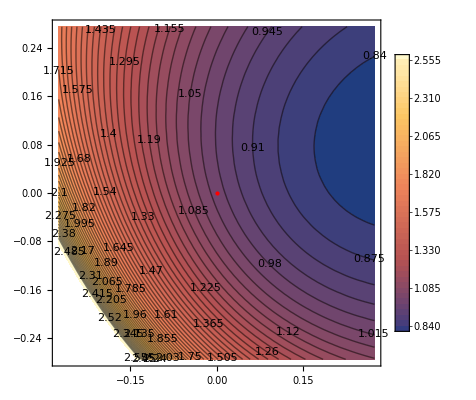

```mathematica
ContourPlot[ ratHGT[{x1,x2}]/ratHGT[{0.0,0.0}],{x1,-ϵ/4,ϵ/4},{x2,-ϵ/4,ϵ/4},
Contours->50,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic]
```

```mathematica
TabView[{
"Speed"->ContourPlot[ rho[{x1,x2}],{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Contours->20,
Epilog->{Red, Point[{0,0}]},
PerformanceGoal->"Speed",
ContourLabels->True,PlotLegends->Automatic],
"Quality"->ContourPlot[ rho[{x1,x2}],{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Epilog->{Red, Point[{0,0}],Green,Circle[{0,0},ϵ]},
Contours->20,
PerformanceGoal->"Quality",
ContourLabels->True,PlotLegends->Automatic]
}]
```

12

The radius of the Trust Region is controlled by 
	ρ=(f(x)-f(x+p))/(m(0)-m(p))
I want to plot this for the example above.

```mathematica
Log[0.01]/Log[0.8]
```

20.6377

```mathematica
D[f[{x,y}],{{x,y}}]-{D[f[{x,y}],x],D[f[{x,y}],y]}
```

{0.,0}

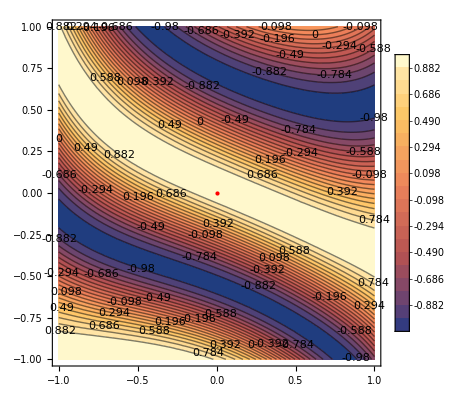

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

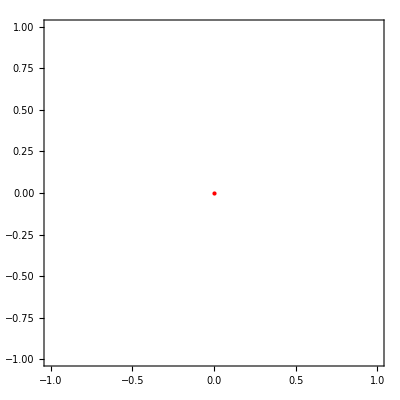

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[f]
f[{x_,y_}]:= Cos[1.9 +Cos[x^2-y]+2.0x+5.0Cos[ x]y]
f0=f[{0.0,0.0}];
grad=D[f[{x,y}]{{x,y},1}]/.{x->0.0,y->0.0};
Hess=D[f[{x,y}],{{x,y},2}]/.{x->0.0,y->0.0};
ContourPlot[f[{x,y}]/f0,{x, -1,1},{y,-1,1},
PlotLegends->Automatic,Contours->20,ContourLabels->True,Epilog->{Red, Point[{0,0}]}]
ContourPlot[f[{x,y}]-(f0+grad.{x,y}+0.5 {x,y}.Hess.{x,y}),{x, -1,1},{y,-1,1},
PlotLegends->Automatic,Contours->20,ContourLabels->True,Epilog->{Red, Point[{0,0}]}]
ContourPlot[f[{x,y}]-(f0+grad.{x,y}),{x, -1,1},{y,-1,1},
PlotLegends->Automatic,Contours->20,ContourLabels->True,Epilog->{Red, Point[{0,0}]}]
```

```mathematica
Expand[f0+grad.{x,y}+0.5 {x,y}.Hess.{x,y}]
Expand[g[{x,y}]]
```

-0.32329-9.32482 x+15.6959 x^2-3.71611 y+12.5102 x y+6.20888 y^2

-0.32329-9.32482 x+15.6959 x^2-3.71611 y+12.5102 x y+185.485 x^2 y+6.20888 y^2+63.1062 x y^2-340.682 x^2 y^2

```mathematica
Eigenvalues[DDF]
{QVal,QSub}=FindMinimum[{Abs[0.5 {x1,x2}.DDF.{x1,x2}+DF.{x1,x2}+F]/F, x1^2+x2^2<0.9},{x1,x2}]
FindMinimum[{Abs[DF.{x1,x2}+F]/F, x1^2+x2^2<0.9},{x1,x2}]
```

{-0.0911667,0.0803622}

{0.926838,{x1→-0.0101622,x2→0.948628}}

{0.917633,{x1→0.835189,x2→0.449953}}

```mathematica
DF
```

{0.0611969,0.0611969}

```mathematica
DDF//MatrixForm
```

(-0.0880433 | -0.0660895
-0.0660895 | 0.133503)

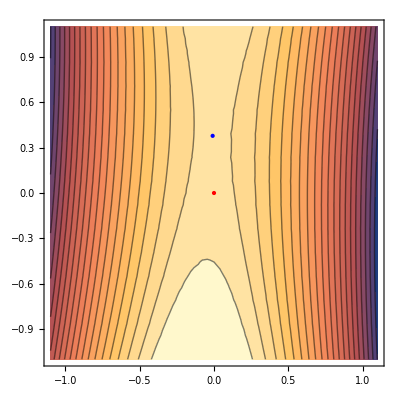

```mathematica
ContourPlot[ 0.5 {x1,x2}.DDF.{x1,x2}+DF.{x1,x2}+F,{x1,-ϵ,ϵ},{x2,-ϵ,ϵ},
Contours->20,
Epilog->{{Red,Point[{0.0,0.0}]},{Blue,Point[LinearSolve[DDF,-DF]]}}]
```